```mathematica
vars=ReadList["out.txt", Number,10000];
{Mean[vars],Variance[vars], Mean[vars]-0.5, Variance[vars]-0.08333}
```

{0.503787,0.0834548,0.00378673,0.000124847}

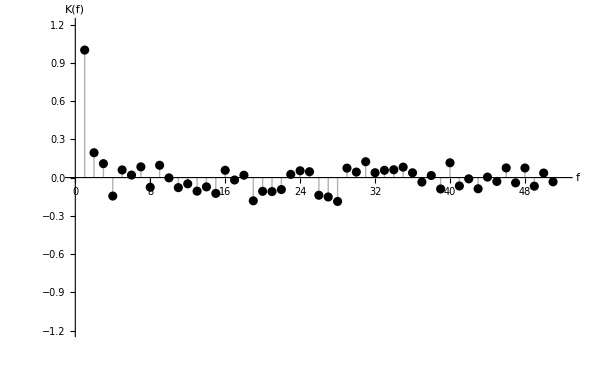

```mathematica
ListPlot[CorrelationFunction[vars,{50}],Filling->Axis,PlotRange->{ {0, 52},{-1.2,1.2}},BaseStyle->{FontFamily->"Cambria", FontSize->14, FontSlant->Italic}, AxesStyle->Arrowheads[{0, 0.03}], AxesOrigin->{0, 0},AxesLabel->{"f","K(f)"}, PlotStyle->Black]
```

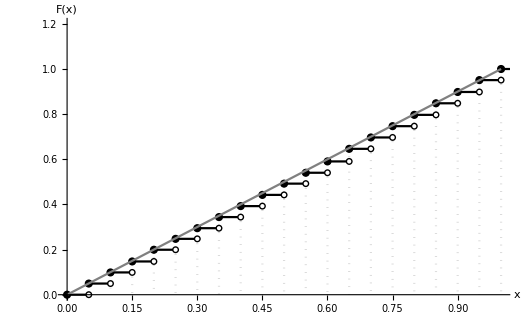

```mathematica
{DiscretePlot[CDF[EmpiricalDistribution[vars],x],{x,0,1,.05}, BaseStyle->{FontFamily->"Cambria", FontSize->14, FontSlant->Italic},AxesStyle->Arrowheads[{0, 0.03}], ExtentSize->Right,Filling->None, ExtentMarkers->{"Filled","Empty"}, PlotStyle->Black,AxesLabel->{"x","F(x)"}, PlotRange->{0, 1.2}], DiscretePlot[CDF[EmpiricalDistribution[vars],x],{x,0,1,.05}, PlotStyle->Dotted, PlotTheme->"Monochrome"]};
Show[%, Plot[CDF[UniformDistribution[], x], {x, 0, 1}, PlotStyle->Gray]]
```

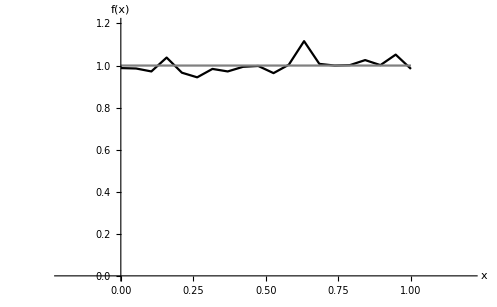

```mathematica
Show[ListLinePlot[BinCounts[vars, {0, 1,0.05}]/500, PlotRange->{{-0.2, 1.2},{0, 1.2}},BaseStyle->{FontFamily->"Cambria", FontSize->14, FontSlant->Italic},AxesStyle->Arrowheads[{0, 0.03}],AxesLabel->{"x","f(x)"}, PlotStyle->Black, DataRange->{0, 1}], Plot[PDF[UniformDistribution[], x], {x, 0, 1}, PlotStyle->Gray]]
```

```mathematica
n=10000;m=4;
(*vars=RandomVariate[DiscreteUniformDistribution[{0, 2^m-1}], n];*)
vars=ReadList["out1.txt", Number,10000];
Counts[vars]
2^m/n Sum[(Counts[vars][[i]]-n/2^m)^2, {i, 1, 2^m}]//N
2^m-1
```

<|1→619,6→643,9→587,7→623,11→636,8→667,3→584,14→620,12→608,15→630,5→613,4→675,10→611,13→638,2→617,0→629|>

14.0832

15

0.493618

```mathematica
Mean[DiscreteUniformDistribution[{0, 1}]]//N
```

0.5